```mathematica
Series[1/(ⅈ ω Q Sqrt[C/L]+Q^2/R^2 L-ω^2 Q^4 C^2/R^4),{Q,0,1}]
```

-ⅈ/(√(C/L) ω Q)+L^2/(C R^2 ω^2)+(ⅈ L^3 Q)/(C √(C/L) R^4 ω^3)+O[Q]^2

```mathematica
Series[1/(ⅈ ω Q Sqrt[C/L]+Q^2/R^2 L-ω^2 Q^4 C^2/R^4),{Q,Infinity,4}]
```

-R^4/(C^2 ω^2 Q^4)+O[1/Q]^5

```mathematica
R1=400;C1=4;L1=16;
```

```mathematica
R2=1;L2=1;C2=1;
```

```mathematica
R3=25;C3=4;L3=16;
```

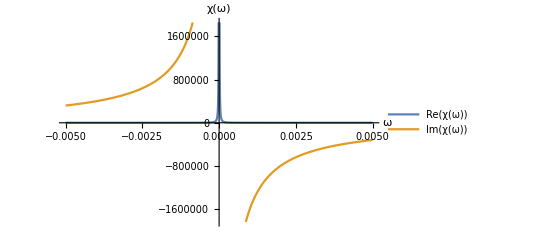

```mathematica
Plot[{L1^2/(C1 R1^2 ω^2),L1^4/(ω^3 R1^5 C1^2)-(L1 R1)/(ω C1)}, {ω,-0.005,0.005},AxesLabel->{ω,χ[ω]},PlotLegends->{Re[χ[ω]],Im[χ[ω]]},Ticks->{None}]
```

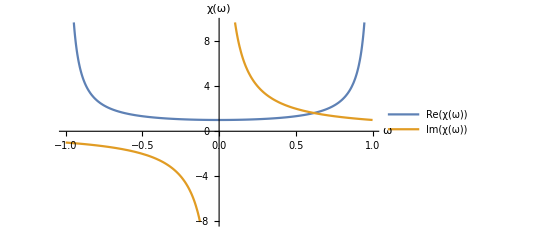

```mathematica
Plot[{1/(-ω^2 L2^2+1/C2),1/(ω R2)}, {ω,-1,1},AxesLabel->{ω,χ[ω]},PlotLegends->{Re[χ[ω]],Im[χ[ω]]},Ticks->{None}]
```

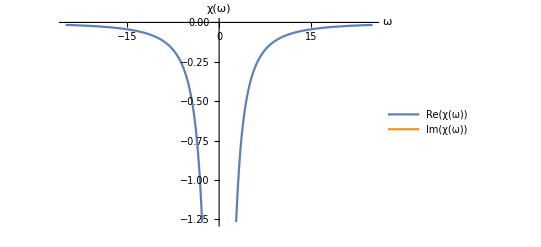

```mathematica
Plot[{-R3^2/(ω^2 L3 C3),None}, {ω,-25,25},AxesLabel->{ω,χ[ω]},PlotLegends->{Re[χ[ω]],Im[χ[ω]]},Ticks->{None}]
```

```mathematica
Solve[ⅈ ω R-ω^2 L^2+1/C==0,ω]
```

{{ω→-(-ⅈ R-(√(4 L^2-C R^2))/(√C))/(2 L^2)},{ω→-(-ⅈ R+(√(4 L^2-C R^2))/(√C))/(2 L^2)}}

```mathematica
ωp=1/10; τ=100;
```

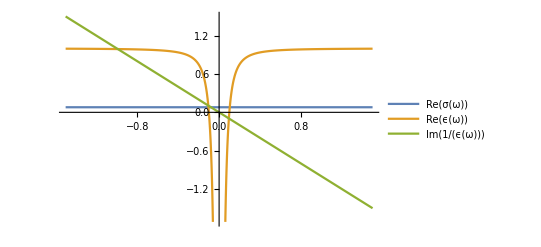

```mathematica
Plot[{(ωp^2 τ)/(4Pi),1-ωp^2/ω^2,-ω/(ωp^2 τ)},{ω,-1.5,1.5},PlotLegends->{Re[σ[ω]],Re[ϵ[ω]],Im[1/ϵ[ω]]},Ticks->{None}]
```